```mathematica
polygonArea[P_] := 1/2*Im[Sum[Conjugate[P[[j]]]*P[[j+1]], {j, 1, Length[P]-1}]];
```

```mathematica
ComplexToReals[z_] := {Re[z], Im[z]};
```

```mathematica
P = {1, I, -1, -I, 1};
```

```mathematica
NumericalRange[A_, eps_:10^-2] :=
Module[{pos, j, k, sys, eigen, eigenx, m, n, H, l, x, y, P, Q, f, z, e, r, d, B}, 
{m, n} = Dimensions[A];
e = 1; r = 2; 
While[e > eps, 
P = {}; Q = {}; 
r = 2*r;
d = 2*Pi/r;
l = {}; x = {};
For[k = 1, k≤ r, ++k ,
B = Exp[I*k*d]*A;
H = (B+ConjugateTranspose[B])/2;
{eigen, eigenx} = Eigensystem[H];
eigen = Re[eigen];
pos = Flatten[Position[eigen, Max[eigen]]][[1]];
(*
For[j = 1, j ≤ n, j++,
If[eigen[[j]] == Max[eigen], 
pos = j;
]
];
*)
AppendTo[l, eigen[[pos]]];
y = ArrayReshape[eigenx[[pos]], {n, 1}];
y = y/Norm[y];
AppendTo[x,y];
];
AppendTo[l ,l[[1]]];
Print[l];
For[k = 1, k ≤ r, ++k,
z = (ConjugateTranspose[x[[k]]].A.x[[k]])[[1]][[1]];
AppendTo[P, N[z]];
f = (l[[k]]*Cos[d]-l[[k+1]])/Sin[d];
z = ( Cos[k*d] - I*Sin[k*d] )*(l[[k]] + I*f);
AppendTo[Q, N[z]];
];
AppendTo[P, P[[1]]];
AppendTo[Q, Q[[1]]];
e = Abs[polygonArea[Q]] - Abs[polygonArea[P]];
(*Print[P];*)
];
Graphics[Polygon[ComplexToReals /@ P]]
]
```

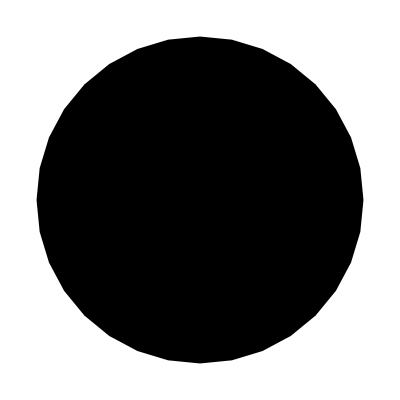

```mathematica
NumericalRange[{{0, 1}, {0, 0}}]
```

```mathematica
A = {{-1, 0, 0, 0, 0}, {0, 1+2I, 0, 0, 0}, {0, 0, 1-2I, 0, 0}, {0, 0, 0, 2+I, 0}, {0, 0, 0, 0, 2-I}};
```

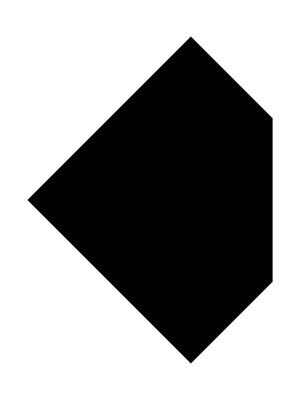

```mathematica
NumericalRange[A, 0.1]
```

```mathematica
NumericalRange[]
```

```mathematica
NumericalRange[{{0, 1}, {1, 0}}]
```

{0.,-1.,0.,1.,0.}

-Graphics-